# Central Limit Theorem

Based on the presentation at https://www.youtube.com/watch?v=JTz4wkD-mxU

### Central Limit Theorem

Note that the Pareto distribution is the most talked about in real life. Not the normal distribution. People are also excited about actuals.

```mathematica
w:=RandomVariate[ParetoDistribution[1,2]]
```

```mathematica
{w,w}//Total
```

4.32565

Consider add up 10000 times. Run the simulation 100 times.

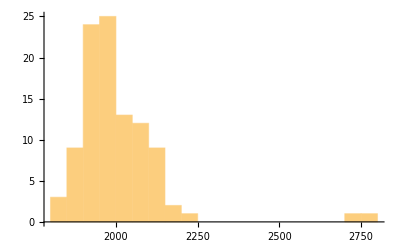

```mathematica
Histogram[Table[Table[w,{1000}]//Total,{100}]]
```

```mathematica
y:=RandomVariate[GammaDistribution[1,1]]
```

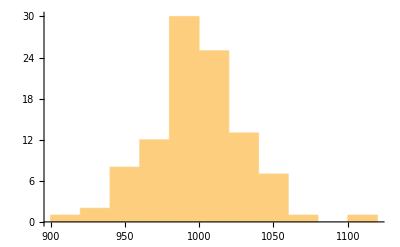

```mathematica
Histogram[Table[Table[y,{1000}]//Total,{100}]]
```

```mathematica
ta=Table[w,{30}];Mean[ta]
```

2.02271

### Other Probability Distributions

```mathematica
r:=RandomVariate[UniformDistribution[]]
```

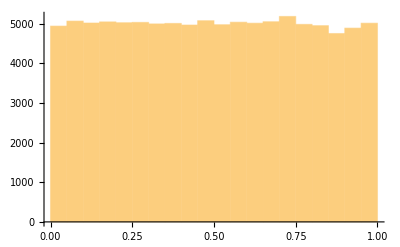

```mathematica
Histogram[Table[r,{10^5}]]
```

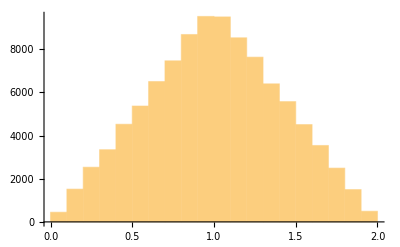

```mathematica
Histogram[Table[Sum[r,{i,1,2}],{10^5}]]
```

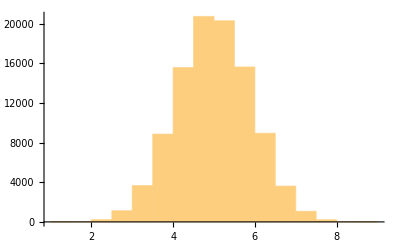

```mathematica
Histogram[Table[Sum[r,{i,1,10}],{10^5}]]
```